# Metodi Monte Carlo a catena di Markov : algoritmo di Metropolis per il TSP (variante senza obbligo di ritorno alla stessa città di partenza): diversi stati iniziali

Vettore di stato iniziale: Rome, Belgrade, Sarajevo, Monaco, Seville, Vilnius, Budapest, Lisbon, Madrid, Naples

Percorso Minimo:

Rome, Naples, Sarajevo, Belgrade, Budapest, Vilnius, Monaco, Madrid, Seville, Lisbon

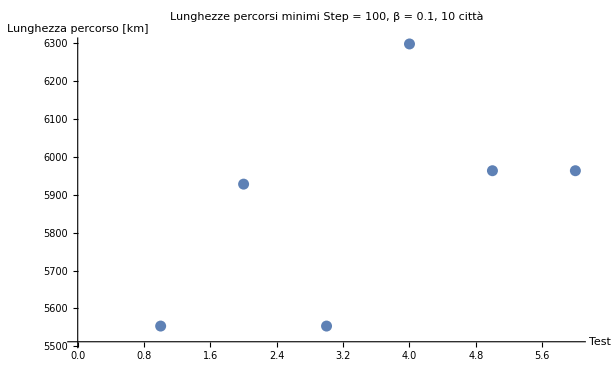

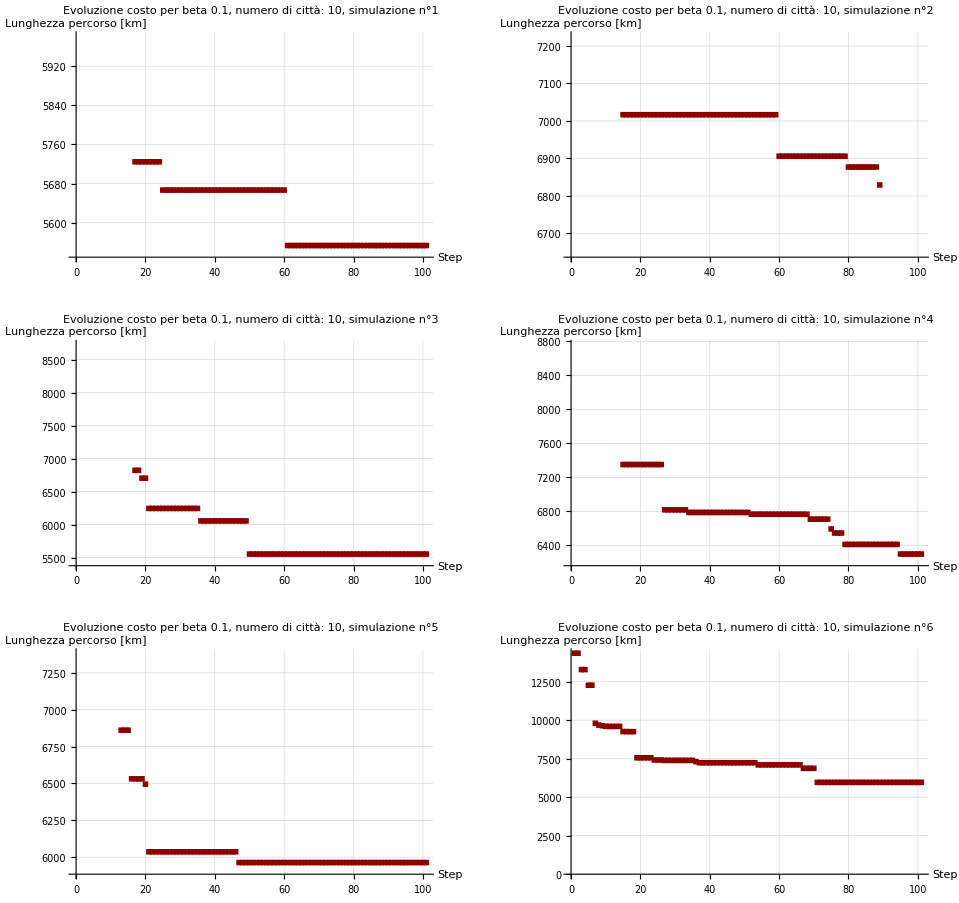

```mathematica
(*Fissato un valore di beta abbastanza alto, cioè un parametro di controllo basso (scarsa possibilità di accettazione di scelte peggiorative) si costruisce un algoritmo basato sulla regola di Metropolis. Ad ogni iterazione, si cambia lo stato iniziale e si osserva se si arriva sempre allo stesso minimo o se si ottengono risultati diversi. Per n piccolo, la funzione distanza presenta un unico minimo che è assoluto; al crescere del numero di città aumenta il numero di minimi relativi, con conseguente perdita di affidabilità dell'algoritmo come metodo di ottimizzazione.*)

(*Numero di città*)n=10;

(*Dati delle città*)
città={<|"nome"->"Amsterdam","lat"->52.3676,"long"->4.9041|>,<|"nome"->"Athens","lat"->37.9838,"long"->23.7275|>,<|"nome"->"Barcelona","lat"->41.3851,"long"->2.1734|>,<|"nome"->"Belgrade","lat"->44.7866,"long"->20.4489|>,<|"nome"->"Berlin","lat"->52.5200,"long"->13.4050|>,<|"nome"->"Bern","lat"->46.9481,"long"->7.4474|>,<|"nome"->"Bratislava","lat"->48.1486,"long"->17.1077|>,<|"nome"->"Brussels","lat"->50.8503,"long"->4.3517|>,<|"nome"->"Bucharest","lat"->44.4268,"long"->26.1025|>,<|"nome"->"Budapest","lat"->47.4979,"long"->19.0402|>,<|"nome"->"Copenhagen","lat"->55.6761,"long"->12.5683|>,<|"nome"->"Dublin","lat"->53.3498,"long"->-6.2603|>,<|"nome"->"Edinburgh","lat"->55.9533,"long"->-3.1883|>,<|"nome"->"Frankfurt","lat"->50.1109,"long"->8.6821|>,<|"nome"->"Geneva","lat"->46.2044,"long"->6.1432|>,<|"nome"->"Helsinki","lat"->60.1695,"long"->24.9354|>,<|"nome"->"Istanbul","lat"->41.0082,"long"->28.9784|>,<|"nome"->"Kiev","lat"->50.4501,"long"->30.5234|>,<|"nome"->"Lisbon","lat"->38.7223,"long"->-9.1393|>,<|"nome"->"Ljubljana","lat"->46.0569,"long"->14.5058|>,<|"nome"->"London","lat"->51.5074,"long"->-0.1278|>,<|"nome"->"Luxembourg","lat"->49.6116,"long"->6.1319|>,<|"nome"->"Madrid","lat"->40.4168,"long"->-3.7038|>,<|"nome"->"Milan","lat"->45.4642,"long"->9.1900|>,<|"nome"->"Monaco","lat"->43.7384,"long"->7.4246|>,<|"nome"->"Moscow","lat"->55.7558,"long"->37.6173|>,<|"nome"->"Munich","lat"->48.1351,"long"->11.5820|>,<|"nome"->"Oslo","lat"->59.9139,"long"->10.7522|>,<|"nome"->"Paris","lat"->48.8566,"long"->2.3522|>,<|"nome"->"Prague","lat"->50.0755,"long"->14.4378|>,<|"nome"->"Reykjavik","lat"->64.1355,"long"->-21.8954|>,<|"nome"->"Riga","lat"->56.9496,"long"->24.1052|>,<|"nome"->"Sarajevo","lat"->43.8563,"long"->18.4131|>,<|"nome"->"Sofia","lat"->42.6977,"long"->23.3219|>,<|"nome"->"Stockholm","lat"->59.3293,"long"->18.0686|>,<|"nome"->"Tallinn","lat"->59.4370,"long"->24.7535|>,<|"nome"->"Tirana","lat"->41.3275,"long"->19.8189|>,<|"nome"->"Valletta","lat"->35.8989,"long"->14.5146|>,<|"nome"->"Vienna","lat"->48.2082,"long"->16.3738|>,<|"nome"->"Vilnius","lat"->54.6872,"long"->25.2797|>,<|"nome"->"Warsaw","lat"->52.2297,"long"->21.0122|>,<|"nome"->"Zagreb","lat"->45.8150,"long"->15.9819|>,<|"nome"->"Zurich","lat"->47.3769,"long"->8.5417|>,<|"nome"->"Seville","lat"->37.3891,"long"->-5.9845|>,<|"nome"->"Naples","lat"->40.8522,"long"->14.2681|>,<|"nome"->"Lyon","lat"->45.7640,"long"->4.8357|>,<|"nome"->"Porto","lat"->41.1579,"long"->-8.6291|>,<|"nome"->"Gothenburg","lat"->57.7089,"long"->11.9746|>,<|"nome"->"Marseille","lat"->43.2965,"long"->5.3698|>,<|"nome"->"Cologne","lat"->50.9375,"long"->6.9603|>};

(*Funzione per creare lo stato iniziale con n città*)
creaStato[città_,n_]:=Module[{scelte},scelte=RandomSample[città[[2;;Length[città]]],n-1];
scelte=Prepend[scelte,<|"nome"->"Rome","lat"->41.8992,"long"->12.5450|>];(*parto sempre da Roma*)scelte]

(*Funzione per calcolare la distanza tra due città*)
distanza[città1_,città2_]:=QuantityMagnitude[GeoDistance[{città1[["lat"]],città1[["long"]]},{città2[["lat"]],città2[["long"]]}]]

(*Funzione per calcolare la distanza totale di un percorso*)
distanzatot[stato_]:=Total[Table[distanza[stato[[i]],stato[[i+1]]],{i,1,Length[stato]-1}]]

(*Funzione per stampare il percorso*)
stampa[stato_]:=StringJoin[Riffle[stato[[All,"nome"]],", "]]

(*Funzione per creare un nuovo stato*)
creaNuovoStato[stato_]:=Module[{rand1,rand2,minRand,maxRand,invertito},{rand1,rand2}=RandomInteger[{2,Length[stato]},2];
{minRand,maxRand}=Sort[{rand1,rand2}];
invertito=Reverse[stato[[minRand;;maxRand]]];
Join[stato[[1;;minRand-1]],invertito,stato[[maxRand+1;;Length[stato]]]]]

(*Funzione per stampare i nomi delle città nel percorso minimo*)
stampaNomiPercorsoMinimo[percorsoMinimo_]:=Module[{nomiCittà},nomiCittà=percorsoMinimo[[All,"nome"]];
Print[StringJoin[Riffle[nomiCittà,", "]]]]

(*Parametri per l'algoritmo di Metropolis*)
rip=10*n; (*numero di ripetizioni per ciascuna simulazione*)
beta=0.1; (*valore di beta*)
nTest=6; (*numero di volte che ripeto il test con il cambio di stato iniziale*)

(*Inizializzazione delle variabili*)
numAccettazioni=Table[0,nTest];
minimi=Table[Infinity,nTest];
storia=Table[Table[0,rip+1],nTest];
memorizzaPercorsi=Table[{},nTest];


(*Creazione dello stato iniziale*)
statoIniz=creaStato[città,n];
Print["Vettore di stato iniziale: ",stampa[statoIniz]];
stato=statoIniz;

(*Algoritmo di Metropolis*)
For[j=1,j<=nTest,j++,stato=creaStato[stato,n];
minimi[[j]]=distanzatot[stato];
memorizzaPercorsi[[j]]=stato;
storia[[j,1]]=distanzatot[stato];
For[i=1,i<=rip,i++,nuovostato=creaNuovoStato[stato];
varCosto=distanzatot[nuovostato]-distanzatot[stato];
If[varCosto<0||Exp[-beta*varCosto]>RandomReal[],stato=nuovostato;
numAccettazioni[[j]]++;
If[distanzatot[stato]<minimi[[j]],minimi[[j]]=distanzatot[stato];
memorizzaPercorsi[[j]]=stato;];];
storia[[j,i+1]]=distanzatot[stato];];]

numMinSim=Position[minimi,Min[minimi]];
numMinSimIndice=numMinSim[[1,1]];
percorsoMinimo=memorizzaPercorsi[[numMinSimIndice]];
Print["Percorso Minimo:"];
stampaNomiPercorsoMinimo[percorsoMinimo];

(*Creazione della stringa con info sulla simulazione*)
info="\nStep = "<>ToString[rip]<>", β = "<>ToString[beta,InputForm]<>", "<>ToString[n]<>" città";

(*Plot dei risultati*)
ListPlot[minimi,AxesLabel->{"Test","Lunghezza percorso [km]"},PlotLabel->"Lunghezze percorsi minimi"<>info]

(*Calcolo della percentuale di accettazione*)
percAccettazione=N[100*(numAccettazioni/rip),3];

(*Lista di grafici per ogni valore di beta*)
grafici=Table[ListPlot[storia[[i]],PlotMarkers->{■,0.001},PlotStyle->{GridLines->Automatic,RGBColor[0.55,0,0]},AxesLabel->{"Step","Lunghezza percorso [km]"},PlotLabel->"Evoluzione costo per beta "<>ToString[beta]<>", numero di città: "<>ToString[n]<>", simulazione n°"<>ToString[i],GridLines->Automatic,Mesh->All,MeshStyle->{Red}],{i,1,nTest}];

(*Mostra i grafici in una griglia*)
GraphicsGrid[Partition[grafici,UpTo[2]]]
```